# Towards a New Data Modelling Architecture

### By Athanassios I. Hatzis, PhD, R&D Software Engineer (C) 17th of March 2015

This is a series of Wolfram Language notebooks that introduce progressively the art of a new innovative, exhilarating, data modelling approach to software developers, architects, data model designers and everyone interested in learning the advantages of applying this method and the main differences from the data models of the past. In Part I We start with terms and constructs that most of us are familiar with from the relational database management systems and we continue with the terminology and constructs of the new model in Part 2.

## Part1: Representations and Transformations on the Constructs of the Relational Model in Wolfram Language

### Scope

The entity-relational data model (ERDM) is still the most popular data model in database management systems. There are several reason for that, but the main one is the simple and natural way of managing data in tables with rows (records) and columns (attributes). On top of that SQL is a very powerful and easy to learn programming language that covers completely the relational operators on data sets. In this Mathematica notebook various methods of representing the basic constructs of the relational model are demonstrated.

Definitions

## Product Type

```mathematica
ClearAll["Global`*"]
```

```mathematica
Needs["DatabaseLink`"]
```

```mathematica
conn=OpenSQLConnection[JDBC["Microsoft Access(ODBC)","C:\\Temp\\SuppliesCatalogDB.mdb"]];
```

### Wikipedia Extract

“In programming languages and type theory, a product of types is another, compounded, type in a structure. The “operands” of the product are types, and the structure of a product type is determined by the fixed order of the operands in the product. An instance of a product type retains the fixed order, but otherwise may contain all possible instances of its primitive data types. The expression of an instance of a product type will be a tuple, and is called a “tuple type” of expression. A product of types is a direct product of two or more types.”

### Example

Integer x String x Colour. In Wolfram Language an instance, p1, of such a type is represented with a list abstract data type. In Wolfram Language we can write

```mathematica
partInstanceAsList={991,"Left Handed Bacon Stretcher Cover",Red}
```

{991,Left Handed Bacon Stretcher Cover,-Graphics-}

And to check/verify the type for each element of the list we apply the function Head to p1

```mathematica
Head /@ partInstanceAsList
```

{Integer,String,RGBColor}

## Tuple or record or row

### Wikipedia Extract

“A tuple is an ordered list of elements. In mathematics, an n-tuple is a sequence (or ordered list) of n elements, where n is a non-negative integer. In computer science, tuples are directly implemented as product types in most functional programming languages. More commonly, they are implemented as record types, where the components are labeled instead of being identified by position alone. This approach is also used in relational algebra.”

“In database theory, the relational model uses a tuple definition similar to tuples as functions, but each tuple element is identified by a distinct name, called an attribute, instead of a number; this leads to a more user-friendly and practical notation. A tuple in the relational model is formally defined as a finite function that maps attributes to values. In this notation, attribute–value pairs may appear in any order.”

### Example

( partID : 991, partName : “Left Handed Bacon Stretcher Cover”, partColor : Red )

In Wolfram Language record abstract data structure is usually represented with the Assocation function, i.e. a symbolically indexed list of rules (key->value  pairs).

```mathematica
partInstanceAsAssociation=Association[partID->991,partName-> "Left Handed Bacon Stretcher Cover",partColor->Red]
```

<|partID→991,partName→Left Handed Bacon Stretcher Cover,partColor→-Graphics-|>

And we can take a list of values in the following way

```mathematica
Values[partInstanceAsAssociation]
```

{991,Left Handed Bacon Stretcher Cover,-Graphics-}

or take a list of rules (key->value) pairs

```mathematica
partInstanceAsAssociation //Normal
```

{partID→991,partName→Left Handed Bacon Stretcher Cover,partColor→-Graphics-}

## Attribute or field or column

### Wikipedia Extract

“The basic relational building block is the domain or data type, usually abbreviated nowadays to type. A tuple is an ordered set of attribute values. An attribute is an ordered pair of attribute name and type name. An attribute value is a specific valid value for the type of the attribute. This can be either a scalar value or a more complex type. A domain describes the set of possible values for a given attribute, and can be considered a constraint on the value of the attribute. Mathematically, attaching a domain to an attribute means that any value for the attribute must be an element of the specified set. Constraints make it possible to further restrict the domain of an attribute.”

### Example

In our example, two of our attributes partID, integer data type and partName, string data type take scalar values. The partColor attribute is of complex type, RGBColor.

```mathematica
Apply[Rule,Thread[{Keys[partInstanceAsAssociation],Head /@ partInstanceAsList}],{1}]
```

{partID→Integer,partName→String,partColor→RGBColor}

### Important Notice

Attribute can be seen as a mapping function. It maps a tuple to a value. For example, what is the color of the part. We can define a function where we pass a single argument which is  the association representation of the tuple and we return the specific value of the key.

Turn the keys of the association to functions, return the specific key of association instance as the value of the attribute

```mathematica
isIdentifierOf[assoc_]:=assoc[partID]
```

```mathematica
isNameOf[assoc_]:=assoc[partName]
```

```mathematica
isColorOf[assoc_]:=assoc[partColor]
```

```mathematica
{isIdentifierOf[partInstanceAsAssociation],isNameOf[partInstanceAsAssociation],isColorOf[partInstanceAsAssociation]}
```

{991,Left Handed Bacon Stretcher Cover,-Graphics-}

## Relation (Base relval)

### Wikipedia Extract

“In the relational model, a relation is a (possibly empty) finite set of tuples all having the same finite set of attributes.This set of attributes is more formally called the sort of the relation, or more casually referred to as the set of column names. A tuple is usually implemented as a row in a database table. The fundamental assumption of the relational model is that all data is represented as mathematical n-ary relations, an n-ary relation being a subset of the Cartesian product of n domains. In the mathematical model, reasoning about such data is done in two-valued predicate logic, meaning there are two possible evaluations for each proposition: either true or false (and in particular no third value such as unknown, or not applicable, either of which are often associated with the concept of NULL). Data are operated upon by means of a relational calculus or relational algebra, these being equivalent in expressive power.

A relation is defined as a set of n-tuples. In both mathematics and the relational database model, a set is an unordered collection of unique, non-duplicated items. A table is an accepted visual representation of a relation; a tuple is similar to the concept of a row. It is a set of tuples sharing the same attributes; a set of columns and rows. A relvar is a named variable of some specific relation type, to which at all times some relation of that type is assigned, though the relation may contain zero tuples.”

### Predicates and the Closed World Assumption

“A relation consists of a heading and a body. A heading is a set of attributes. A body (of an n-ary relation) is a set of n-tuples. The heading of the relation is also the heading of each of its tuples. The body of a relation is sometimes called its extension. This is because it is to be interpreted as a representation of the extension of some predicate, this being the set of true propositions that can be formed by replacing each free variable in that predicate by a name (a term that designates something). There is a one-to-one correspondence between the free variables of the predicate and the attribute names of the relation heading. Each tuple of the relation body provides attribute values to instantiate the predicate by substituting each of its free variables. The result is a proposition that is deemed, on account of the appearance of the tuple in the relation body, to be true. Contrariwise, every tuple whose heading conforms to that of the relation, but which does not appear in the body is deemed to be false. This assumption is known as the closed world assumption: it is often violated in practical databases, where the absence of a tuple might mean that the truth of the corresponding proposition is unknown.”

### Example

```mathematica
SQLSelect[conn,"Parts","ShowColumnHeadings"->True]//TableForm
```

pid | pname | pcolor
991 | Left Handed Bacon Stretcher Cover | Red
992 | Smoke Shifter End | Black
993 | Acme Widget Washer | Red
994 | Acme Widget Washer | Silver
995 | I Brake for Crop Circles Sticker | Translucent
996 | Anti-Gravity Turbine Generator | Cyan
997 | Anti-Gravity Turbine Generator | Magenta
998 | Fire Hydrant Cap | Red
999 | 7 Segment Display | Green

```mathematica
SQLSelect[conn,"Parts","ShowColumnHeadings"->True]
```

{{pid,pname,pcolor},{991,Left Handed Bacon Stretcher Cover,Red},{992,Smoke Shifter End,Black},{993,Acme Widget Washer,Red},{994,Acme Widget Washer,Silver},{995,I Brake for Crop Circles Sticker,Translucent},{996,Anti-Gravity Turbine Generator,Cyan},{997,Anti-Gravity Turbine Generator,Magenta},{998,Fire Hydrant Cap,Red},{999,7 Segment Display,Green}}

## View or Result Set (Derived relvar)

### Wikipedia Extract

“In a relational database, all data are stored and accessed via relations. Relations that store data are called “base relations”, and in implementations are called “tables”. Other relations do not store data, but are computed by applying relational operations to other relations. These relations are sometimes called “derived relations”. In implementations these are called “views” or “queries”.”

### Example

```mathematica
queryString="
SELECT Catalog.catsid, Suppliers.sname, Catalog.catpid, Parts.pname, Parts.pcolor, Catalog.catcost
FROM Suppliers INNER JOIN (Parts INNER JOIN [Catalog] ON Parts.pid = Catalog.[catpid]) ON Suppliers.sid = Catalog.[catsid]
WHERE (((Catalog.catpid)=998))
ORDER BY Catalog.catcost;";
```

```mathematica
SQLExecute[conn,queryString,"ShowColumnHeadings"->True]//TableForm
```

catsid | sname | catpid | pname | pcolor | catcost
1082 | Big Red Tool and Die | 998 | Fire Hydrant Cap | Red | 7.95
1081 | Acme Widget Suppliers | 998 | Fire Hydrant Cap | Red | 11.7
1083 | Perfunctory Parts | 998 | Fire Hydrant Cap | Red | 12.5
1084 | Alien Aircaft Inc. | 998 | Fire Hydrant Cap | Red | 48.6

## Database

### Wikipedia Extract

“Each database is a collection of related tables; these are also called relations, hence the name “relational database”. Each table is a physical representation of an entity or object that is in a tabular format consisting of columns and rows.”

### Example

```mathematica
SQLTableNames[conn]
```

{Catalog,Parts,Suppliers}

```mathematica
SQLTableInformation[conn,"ShowColumnHeadings"->True]//TableForm
```

TABLE_CAT | TABLE_SCHEM | TABLE_NAME | TABLE_TYPE | REMARKS
C:\Temp\SuppliesCatalogDB.mdb | Null | Catalog | TABLE | Null
C:\Temp\SuppliesCatalogDB.mdb | Null | Parts | TABLE | Null
C:\Temp\SuppliesCatalogDB.mdb | Null | Suppliers | TABLE | Null

```mathematica
SQLTableNames[conn,"TableType"->SQLTableTypeNames[conn]]
```

{MSysAccessObjects,MSysAccessXML,MSysACEs,MSysIMEXColumns,MSysIMEXSpecs,MSysNameMap,MSysNavPaneGroupCategories,MSysNavPaneGroups,MSysNavPaneGroupToObjects,MSysNavPaneObjectIDs,MSysObjects,MSysQueries,MSysRelationships,Catalog,Parts,Suppliers,View998Suppliers,ViewAll}

## Entity-Relationship (ER) Modeling

### Wikipedia Extract

“An entity–relationship model is a systematic way of describing and defining a business process. The process is modeled as components (entities) that are linked with each other by relationships that express the dependencies and requirements between them. Entities may have various properties (attributes) that characterize them. Diagrams created to represent these entities, attributes, and relationships graphically are called entity–relationship diagrams.”

### ER / Relational Terms Equivalence

Entity Type 	- Relation (Table, Base relvar)
Entity		- Tuple
Attribute	- Attribute (column)
Relationship	- View (Result set or Derived relvar)

### EER (Enhanced Entity-Relationship) Model

“The EER model includes all of the concepts introduced by the ER model. Additionally it includes the concepts of a subclass and superclass (Is-a), along with the concepts of specialization and generalization. Furthermore, it introduces the concept of a union type or category, which is used to represent a collection of objects that is the union of objects of different entity types.”

## Constrains

### Wikipedia Extract

“Constraints provide one method of implementing business rules in the database. SQL implements constraint functionality in the form of check constraints. Constraints restrict the data that can be stored in relations. These are usually defined using expressions that result in a boolean value, indicating whether or not the data satisfies the constraint.

Constraints can apply to single attributes, to a tuple (restricting combinations of attributes) or to an entire relation. Since every attribute has an associated domain, there are constraints (domain constraints). The two principal rules for the relational model are known as entity integrity and referential integrity.

In ER modeling we have two types of constrains that are placed on relationships, cardinality and participation. A cardinality constraint places a limit on the number of relationships an entity may participate in at any given time.”

Table and Record in Wolfram Language

The basic construct of the ER model is the record, a table can be defined as a list of records.

## Representation of a Record in Wolfram Language

### List Representations

You need to maintain two ordered lists, one for the data values and another one for the semantics, i.e. the attribute/column names.

```mathematica
partInstanceAsList
```

{991,Left Handed Bacon Stretcher Cover,-Graphics-}

```mathematica
attributes={"pid","pname","pcolor"}
```

{pid,pname,pcolor}

But you can combine the two lists in one list of rules with the following command

```mathematica
Thread[Rule[attributes,partInstanceAsList]]
```

{pid→991,pname→Left Handed Bacon Stretcher Cover,pcolor→-Graphics-}

A Rule is the equivalent of a key-value pair, but it is more powerful because in Wolfram Language it is the basic mechanism that is used in transformations. Nevertheless for lookup operations and updating Wolfram researchers added a more powerful construct that is called Association, see below.

### Graph Representation with triplets (RDF)

Let us call a specific part instance partXYZ, if we represent this as the subject resource of a triplet, the list of attributes as the predicates and the list of values as the objects we can take the following triplets adding example namespaces

```mathematica
subject=Table["http://example.org/resource/partXYZ",{3}];
predicate = StringJoin["http://example.org/attribute/",#]&/@attributes;
object = partInstanceAsList;
```

```mathematica
Transpose[{subject,predicate,object}]//TableForm
```

http://example.org/resource/partXYZ | http://example.org/attribute/pid | 991
http://example.org/resource/partXYZ | http://example.org/attribute/pname | Left Handed Bacon Stretcher Cover
http://example.org/resource/partXYZ | http://example.org/attribute/pcolor | -Graphics-

#### Directed Graph

```mathematica
graphData =DirectedEdge[#,partXYZ]&/@Values[partInstanceAsAssociation]
```

{991->partXYZ,Left Handed Bacon Stretcher Cover->partXYZ,-Graphics-->partXYZ}

```mathematica
vstyle ={#->Black&/@Values[partInstanceAsAssociation],partXYZ->Red}//Flatten
```

{991→-Graphics-,Left Handed Bacon Stretcher Cover→-Graphics-,-Graphics-→-Graphics-,partXYZ→-Graphics-}

```mathematica
elabels =Apply[Rule,Thread[{graphData,Keys[partInstanceAsAssociation]}],{1}]
```

{991->partXYZ→partID,Left Handed Bacon Stretcher Cover->partXYZ→partName,-Graphics-->partXYZ→partColor}

```mathematica
Graph[graphData,
VertexSize->Medium,VertexStyle->vstyle,VertexLabels->"Name",
EdgeStyle->Thick,EdgeLabels->elabels,EdgeShapeFunction->GraphElementData[{"CarvedArrow","ArrowSize"->.06}],
GraphLayout->"SpringEmbedding"]
```

-Graphics-

We can observe two types of nodes in this kind of graph, URI (RED) node and Literal (BLACK) nodes.

### TreeForm Representation

From the discussion above we saw two abstract data structures that are suitable for tuple representation: the List and the Associative array also known as Map or Dictionary. The equivalent representations in Wolfram Language are the List and the Association functions. In fact, Wolfram Language functions are tree data structures that are created in the memory as a contiguous array of pointers, the first to the head and the rest to its successive elements. Take for example the list we defined, partInstanceAsList, we can present it in a tree form:

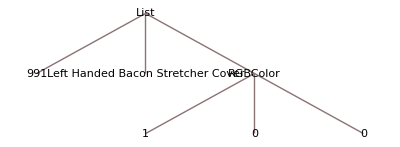

```mathematica
partInstanceAsList //TreeForm
```

That reveals that the symbol Red is set to the result of the function RGBColor with parameters 1,0,0

```mathematica
RGBColor[1,0,0]
```

-Graphics-

```mathematica
Red
```

-Graphics-

### Function Representation

We can represent this triplet, partInstanceAsList as a function with three arguments that take values from the Integer, String and Color domains

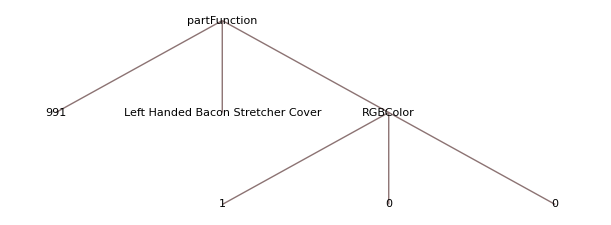

```mathematica
partFunction[991,"Left Handed Bacon Stretcher Cover",Red]//TreeForm
```

### Association Representation

Associations in Wolfram Language are very similar to the Association Type construct of the Topic Map data model. Each defined association is an instance of an association type, e.g. partInstanceAsAssociation, the type of a supplies part. The keys of the association, association role type according to Topic Maps terminology, describe the role type of the values in the association instance. The values of the association, association role players according to Topic Maps terminology, describe the particular instance of the association type. In the following example, we have three role players, the values 991, “Left Handed Bacon Stretcher Cover” and Red that describe a part from a supplies catalog database. Each player has a role type that is important for semantic purposes. The integer number 991, is used as an identifier for the part, its role type is that of an identifier. The string “Left Handed Bacon Stretcher Cover” is used as a name descriptor and the symbol Red is used as the value of the categorical variable color to describe the color of the part.

The command to perform the association of attributes with their values is the following

```mathematica
AssociationThread[attributes->partInstanceAsList]
```

<|pid→991,pname→Left Handed Bacon Stretcher Cover,pcolor→-Graphics-|>

Association is a relatively new fundamental construct in Wolfram Language, it acts like a symbolically indexed list. The main reason for using it is to allow highly efficient lookup and updating and also build complex hierarchical structures and other datasets.

You can easily convert an Association to a list of rules

```mathematica
%//Normal
```

{pid→991,pname→Left Handed Bacon Stretcher Cover,pcolor→-Graphics-}

```mathematica
partInstanceAsAssociation
```

<|partID→991,partName→Left Handed Bacon Stretcher Cover,partColor→-Graphics-|>

```mathematica
Keys[partInstanceAsAssociation]
```

{partID,partName,partColor}

```mathematica
Values[partInstanceAsAssociation]
```

{991,Left Handed Bacon Stretcher Cover,-Graphics-}

### HyperGraph Representation

Although, it is possible to represent a hypergraph by a bipartite graph and follow the RDF (Subject-Predicate-Object) approach  I would like to demonstrate a different perspective that eventually leads to what I named the enhanced hypergraph representation of the relational model that follows in Part 2 of this series.

We will use two lists of rules, one for the attributes and another for the values. Essentially we follow the same principle as with the lists above, we separate the semantics from the data values, i.e. types from instances. This is a critical step in a completely new way of thinking about the data modeling process.

#### List of Rules for Attributes

Take the list of attributes first and add in the beginning of the list another one which we call nexusPart. This is the hyperedge that connects all the other attributes together.

```mathematica
Insert[attributes,"nexusPart",1]
```

{nexusPart,pid,pname,pcolor}

and using a list of rules we take

```mathematica
conceptsRules =Thread[Rule[
Table["nexusPart",{3}],
attributes]]
```

{nexusPart→pid,nexusPart→pname,nexusPart→pcolor}

```mathematica
vstyle ={#->Black&/@attributes,"nexusPart"->Red}//Flatten
```

{pid→-Graphics-,pname→-Graphics-,pcolor→-Graphics-,nexusPart→-Graphics-}

A graphical representation of the list above is the following

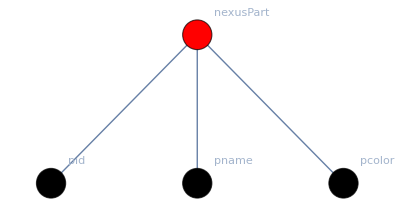

```mathematica
Graph[conceptsRules,VertexSize->Medium,VertexStyle->vstyle,VertexLabels->"Name"]
```

So, in this hypergraph the nexusPart plays the role of the hyperedge with a red color, that connects three hypernodes that represent the attributes (pid, pname, pcol) with a black color.

#### List of Rules for Values

Now we can proceed with the data

```mathematica
partInstanceAsList
```

{991,Left Handed Bacon Stretcher Cover,-Graphics-}

```mathematica
dataRules=Thread[Rule[
Table["nexus991",{3}],
partInstanceAsList]]
```

{nexus991→991,nexus991→Left Handed Bacon Stretcher Cover,nexus991→-Graphics-}

```mathematica
vstyle ={#->Blue&/@partInstanceAsList,"nexus991"->Green}//Flatten
```

{991→-Graphics-,Left Handed Bacon Stretcher Cover→-Graphics-,-Graphics-→-Graphics-,nexus991→-Graphics-}

A graphical representation of the list above is the following

```mathematica
Graph[dataRules,VertexSize->Medium,VertexStyle->vstyle,VertexLabels->"Name"]
```

-Graphics-

And in this hypergraph the nexus991 plays the role of a hyperedge with a green color, that connects three hypernodes that represent the values (991, “Left Handled....”, RED) with a blue color.

#### Summary

We created two handles, we call them nexuses, one at a layer of concepts to represent the head of the record and another at the data layer to represent the body of the record. Provided that we find a way to connect the two layers, we are now in a position to create concept graphs, we will call them maps from now on, that are similar to the ER diagrams that database designers build in RDBMS.

### Property Graph Representation

In the property graph representation, each record becomes an instance of a class that is represented graphically with a node. Attributes of the record are usually embedded in the structure of the node as properties of the class. If we follow our previous example we can take the association representation

```mathematica
partInstanceAsAssociation
```

<|partID→991,partName→Left Handed Bacon Stretcher Cover,partColor→-Graphics-|>

and add an extra handler that refers to that association and represents a key for looking up associations. For example:

```mathematica
"recKey991"->partInstanceAsAssociation
```

recKey991→<|partID→991,partName→Left Handed Bacon Stretcher Cover,partColor→-Graphics-|>

This way the same key can be used to maintain an association of biderectional links to other records through a specific edge. For example part 991 has two suppliers 1081 and 1082

```mathematica
"recKey991"-><|"recKey1082"->"isSupplierOf991","recKey1081"->"isSupplierOf991"|>
```

recKey991→<|recKey1082→isSupplierOf991,recKey1081→isSupplierOf991|>

## Representation of a Table in Wolfram Language

### As a List of Lists

Wolfram Language provides experessions that represent many SQL constructs such as Table (SQLTable, SQLTables, SQLTableNames, SQLTableInformation) and Column (SQLColumn, SQLColumns, SQLColumnNames, SQLColumnInformation). These commands get information about the structure of these constructs.

There are also two styles of commands for working with data: Wolfram Language SQL commands, SQLSelect, SQLUpdate, SQLInsert, etc, for those who are familiar with the language and execution of SQL-Style query commands using SQLExecute statement.

```mathematica
partsList=SQLSelect[conn,"Parts","ShowColumnHeadings"->True]
```

{{pid,pname,pcolor},{991,Left Handed Bacon Stretcher Cover,Red},{992,Smoke Shifter End,Black},{993,Acme Widget Washer,Red},{994,Acme Widget Washer,Silver},{995,I Brake for Crop Circles Sticker,Translucent},{996,Anti-Gravity Turbine Generator,Cyan},{997,Anti-Gravity Turbine Generator,Magenta},{998,Fire Hydrant Cap,Red},{999,7 Segment Display,Green}}

```mathematica
partsList//TableForm
```

pid | pname | pcolor
991 | Left Handed Bacon Stretcher Cover | Red
992 | Smoke Shifter End | Black
993 | Acme Widget Washer | Red
994 | Acme Widget Washer | Silver
995 | I Brake for Crop Circles Sticker | Translucent
996 | Anti-Gravity Turbine Generator | Cyan
997 | Anti-Gravity Turbine Generator | Magenta
998 | Fire Hydrant Cap | Red
999 | 7 Segment Display | Green

```mathematica
suppliersList=SQLSelect[conn,"Suppliers","ShowColumnHeadings"->True];
```

```mathematica
catalogList=SQLSelect[conn,"Catalog","ShowColumnHeadings"->True];
```

### As a List of Associations or Dataset Construct

#### List of Associations

Here we demonstrate how we can arrive to a list of associations from a list of lists of data in the previous section. First we split the header, column attributes, from the body, records of data.

```mathematica
attributes =partsList[[1]]
```

{pid,pname,pcolor}

```mathematica
data =partsList[[2;;]]
```

{{991,Left Handed Bacon Stretcher Cover,Red},{992,Smoke Shifter End,Black},{993,Acme Widget Washer,Red},{994,Acme Widget Washer,Silver},{995,I Brake for Crop Circles Sticker,Translucent},{996,Anti-Gravity Turbine Generator,Cyan},{997,Anti-Gravity Turbine Generator,Magenta},{998,Fire Hydrant Cap,Red},{999,7 Segment Display,Green}}

Now we are in a position to create the first association

```mathematica
AssociationThread[attributes->data[[1]]]
```

<|pid→991,pname→Left Handed Bacon Stretcher Cover,pcolor→Red|>

Then generalize the method to transofrm the list of records to a list of associations

```mathematica
AssociationThread[attributes->#]&/@data//TableForm
```

<|pid→991,pname→Left Handed Bacon Stretcher Cover,pcolor→Red|>
<|pid→992,pname→Smoke Shifter End,pcolor→Black|>
<|pid→993,pname→Acme Widget Washer,pcolor→Red|>
<|pid→994,pname→Acme Widget Washer,pcolor→Silver|>
<|pid→995,pname→I Brake for Crop Circles Sticker,pcolor→Translucent|>
<|pid→996,pname→Anti-Gravity Turbine Generator,pcolor→Cyan|>
<|pid→997,pname→Anti-Gravity Turbine Generator,pcolor→Magenta|>
<|pid→998,pname→Fire Hydrant Cap,pcolor→Red|>
<|pid→999,pname→7 Segment Display,pcolor→Green|>

#### The Structured Dataset Construct of Wolfram Language

Finally with the special Dataset construct that the Wolfram Language provides we can take a dataset. Dataset has the interesting property that can represent not only multidimensional arrays of data, but also data with arbitrary hierarchical structure. The second interesting property is that we can apply various operators such as part, filtering, aggregation, subquery and arbitrary functions directly on the dataset. A few examples to demonstrate these:

```mathematica
partsDataset=Dataset[AssociationThread[attributes->#]&/@data]
```

```mathematica
suppliersDataset=Dataset[AssociationThread[suppliersList[[1]]->#]&/@suppliersList[[2;;]]]
```

```mathematica
catalogDataset=Dataset[AssociationThread[catalogList[[1]]->#]&/@catalogList[[2;;]]]
```

```mathematica
Select[catalogDataset,#catpid==998&];
```

Or equally

```mathematica
catalogDataset[Select[#catpid==998&]]
```

```mathematica
catalogDataset[GroupBy[Key["catpid"]]];
```

Or equally

```mathematica
catalogDataset[GroupBy[{#catpid}&]]
```